-Graphics-

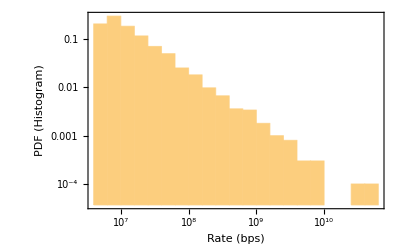

```mathematica
f[α_,β_]:=β*(1/(1-RandomVariate[UniformDistribution[{0.001,0.999}]]))^(1/α);
g[α_,β_,x_]:=Min[40*10^9,x*β*(1/(1-RandomVariate[UniformDistribution[]]))^(1/α)];
descriptivestatistics[data_]:={{"Mean","Median","Stdv.","Skewness","Kurtosis"},{Mean[data],Median[data],StandardDeviation[data],Skewness[data],Kurtosis[data]}}//Transpose//Grid//Panel;
list=Table[(
Subscript[l, i]=Table[g[1.0256410256410255,10^6,5*10^(i-1)],{j,10000}];
Subscript[h, i] = GraphicsGrid[{{Histogram[Subscript[l, i],"Log","LogProbability",FrameLabel->{"Rate (bps)","PDF (Histogram)"},Frame->True],descriptivestatistics@Subscript[l, i]}},ImageSize->Full]
),{i,1,4}];
list[[1]]
```

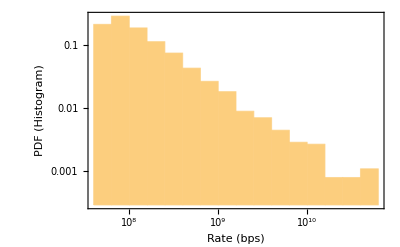

```mathematica
list[[2]]
```

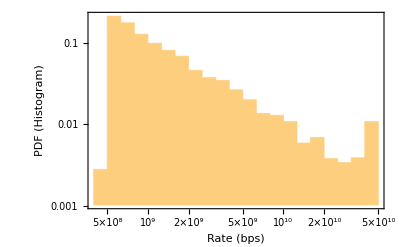

```mathematica
list[[3]]
```

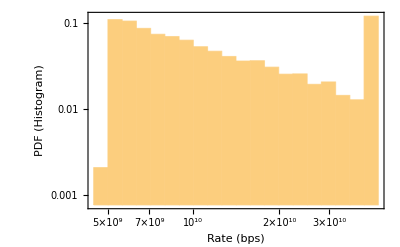

```mathematica
list[[4]]
```

```mathematica
Subscript[list, 40]={{10,46.44561},{20,90.5256},{30,132.91443914439},{40,173.94772},{50,213.8356},{60,252.74132965319},{70,290.72943647182},{80,327.94616},{90,364.41211412114}};
Subscript[list, 400] ={{10,124.21595},{20,217.72968},{30,295.62550625506},{40,362.92448},{50,422.20425},{60,475.12048481939},{70,522.72411620581},{80,565.85456},{90,605.146}};
Subscript[list, 4000] ={{10,301.60049},{20,413.12056},{30,466.59103591036},{40,494.55032},{50,510.04655},{60,518.95721828873},{70,524.27616380819},{80,527.63152},{90,529.80847808478}};
Subscript[list, 40000] ={{10,140.30559},{20,141.39894},{30,141.91869918699},{40,142.43528},{50,142.95135},{60,143.46573862955},{70,143.98809940497},{80,144.50424},{90,145.0202502025}};

ListPlot[{Callout[Subscript[list, 40],"Mean = 40 M"],Callout[Subscript[list, 400],"Mean = 400 M"],Callout[Subscript[list, 4000],"Mean = 2.5 G"],Callout[Subscript[list, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of flowlets that seen at the window"}]
```

-Graphics-

```mathematica
Subscript[newlist, 40]={{10,4426.63962},{20,4428.44124},{30,4430.2349923499},{40,4432.05148},{50,4433.86395},{60,4435.5899435977},{70,4437.3750787539},{80,4439.26128},{90,4441.0571505715}};
Subscript[newlist, 400] ={{10,1130.41252},{20,1132.442},{30,1134.4671946719},{40,1136.50688},{50,1138.54415},{60,1140.5311412456},{70,1142.5686384319},{80,1144.62856},{90,1146.6562865629}};
Subscript[newlist, 4000] ={{10,530.49309},{20,532.81376},{30,535.14094140941},{40,542.10026401056},{50,539.78855},{60,542.10026401056},{70,544.41575078754},{80,546.75304},{90,549.09144091441}};
Subscript[newlist, 40000] ={{10,142.9596},{20,145.54734},{30,148.13356133561},{40,150.72184},{50,153.30955},{60,155.89523580943},{70,158.48925446272},{80,161.07736},{90,163.66474664747},{1000,424.6548}};

ListPlot[{Callout[Subscript[newlist, 40],"Mean = 40 M"],Callout[Subscript[newlist, 400],"Mean = 400 M"],Callout[Subscript[newlist, 4000],"Mean = 2.5 G"],Callout[Subscript[newlist, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of living flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of living flowlets"}]
```

-Graphics-

```mathematica
distOfSizes = {0.01728594,
0.005140236,
0.005232129,
0.032341695,
0.044879491,
0.231028785,
0.179568695,
0.126417652,
0.130605671,
0.116946187,
0.067761784,
0.008431136,
0.003078399,
0.005519292,
0.009625739,
0.016137169
};
plotData[file_,withElephant_]:=Module[{str,listStrings,missCount,outOfOrder,sum,l,x},(
str = Import[file];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];
outOfOrder = ToExpression[ StringDrop[listStrings[[2]],{-3}]];

sizes = {1177 ,4264 ,15443 ,28000 ,37323 ,51067 ,74908 ,93293 ,141819 ,237853 ,573344 ,2076744 ,7521945 ,27244995 ,98686787 ,223092956};

sum = Total[Map[#[[3]]&,missCount]];
data = Map[{#[[1]],100*#[[2]],#[[3]]}&,outOfOrder];
d=Map[Module[{s},s=#;Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,sizes];
(*The miss count:*)
missCountList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,missCount];
If[withElephant == True,rtt = (5.8)*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt;
missHopPlots = Map[Module[{s,oneSzie,oneSum,oneMean},s=#;
oneSzie = Select[missCount,(#[[1]]==s)&];
oneSum = Total[Map[#[[3]]&,oneSzie]];
oneMean = N[Total[Map[#[[4]]&,oneSzie]]/oneSum];
Labeled[ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT\nrate = " <> ToString[pivot/10^6] <> " Mbps",Tiny],Automatic]}],"Avg miss hop = " <> ToString[oneMean]]
]&,sizes];
Return[{missHopPlots,N[Total[Map[#[[4]]&,missCount]]/sum]}];

(*Size distribution validation:*)
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}]];
Print[BarChart[N[1/Total[d]*d],ChartLabels->sizes,PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]];
Print[ListPlot3D[missCountList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Miss count",AxesLabel->{"size (Bytes)","rate (Mbps)","miss count"},PlotRange->{0,4}]];
Print["The mean of the miss count: ",N[Total[Map[#[[4]]&,missCount]]/sum]];


Print[missHopPlots];
Print[Total[missHopPlots]];

hashsize[size_]:=Position[sizes,size][[1]][[1]];
heatMap = ConstantArray[0,{17,40000/100}];
Map[((heatMap[[hashsize[#[[1]]],(#[[2]])/100]] = #[[3]]))&,data3];

outOfOrderList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,outOfOrder];
Print[ListPlot3D[outOfOrderList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Out of order",AxesLabel->{"size (Bytes)","rate (Mbps)","out of oreder"},PlotRange->All]];
Print[Map[Module[{s},s=#;ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[outOfOrderList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s],AxesLabel->{"Rate (Mbps)","Avg out of order"}]]&,sizes]];

Print["The mean of the out of oreder: ",N[Total[Map[(#[[4]])/sum&,outOfOrder]]]];
)]
```

```mathematica
plotData["with 1,1 new.txt",True]
```

{{-Graphics-Avg miss hop = 3.,-Graphics-Avg miss hop = 2.67486,-Graphics-Avg miss hop = 1.7741,-Graphics-Avg miss hop = 1.52726,-Graphics-Avg miss hop = 1.43019,-Graphics-Avg miss hop = 1.32316,-Graphics-Avg miss hop = 1.23693,-Graphics-Avg miss hop = 1.18736,-Graphics-Avg miss hop = 1.12469,-Graphics-Avg miss hop = 1.0722,-Graphics-Avg miss hop = 1.03094,-Graphics-Avg miss hop = 1.00786,-Graphics-Avg miss hop = 0.991164,-Graphics-Avg miss hop = 1.00805,-Graphics-Avg miss hop = 0.996783,-Graphics-Avg miss hop = 0.999886},1.00288}

```mathematica
{p1,av1} = plotData["with 1,1 new.txt",True];
{p2,av2} = plotData["without 1,1 new.txt",False];
{p3,av3} = plotData["with 2,2 new.txt",True];
{p4,av4}= plotData["without 2,2 new.txt",False];
{p5,av5}= plotData["a.txt",True];
{p6,av6}= plotData["a.txt",True];
```

```mathematica
Manipulate[{Labeled[p1[[i]],"With 1,1\n Total Avg miss hop = " <> ToString[av1]],Labeled[p2[[i]],"Without 1,1\n Total Avg miss hop = " <> ToString[av2]],Labeled[p3[[i]],"With 2,2\n Total Avg miss hop = " <> ToString[av3]],Labeled[p4[[i]],"Without 2,2\n Total Avg miss hop = " <> ToString[av4]],Labeled[p5[[i]],"With 10,10\n Total Avg miss hop = " <> ToString[av5]],Labeled[p6[[i]],"Without 10,10\n Total Avg miss hop = " <> ToString[av6]]},{i,1,Length[sizes],1}]
```

```mathematica
{q1,nav1} = plotData["with 1,1.txt",True];
{q2,nav2} = plotData["witout 1,1.txt",False];
{q3,nav3} = plotData["with 2,2.txt",True];
{q4,nav4}= plotData["without 2,2.txt",False];
{q5,nav5}= plotData["with 10,10.txt",True];
{q6,nav6}= plotData["without 10,10.txt",False];
```

```mathematica
Manipulate[{Labeled[q1[[i]],"With 1,1\n Total Avg miss hop = " <> ToString[nav1]],Labeled[q2[[i]],"Without 1,1\n Total Avg miss hop = " <> ToString[nav2]],Labeled[q3[[i]],"With 2,2\n Total Avg miss hop = " <> ToString[nav3]],Labeled[q4[[i]],"Without 2,2\n Total Avg miss hop = " <> ToString[nav4]],Labeled[q5[[i]],"With 10,10\n Total Avg miss hop = " <> ToString[nav5]],Labeled[q6[[i]],"Without 10,10\n Total Avg miss hop = " <> ToString[nav6]]},{i,1,Length[sizes],1}]
```

```mathematica
Manipulate[{Labeled[q1[[i]],"With 1,1\n Total Avg miss hop = " <> ToString[nav1]],Labeled[q2[[i]],"Without 1,1\n Total Avg miss hop = " <> ToString[nav2]],Labeled[q3[[i]],"With 2,2\n Total Avg miss hop = " <> ToString[nav3]],Labeled[q4[[i]],"Without 2,2\n Total Avg miss hop = " <> ToString[nav4]],Labeled[q5[[i]],"With 10,10\n Total Avg miss hop = " <> ToString[nav5]],Labeled[q6[[i]],"Without 10,10\n Total Avg miss hop = " <> ToString[nav6]]},{i,1,Length[sizes],1}]
```

```mathematica
data
```

{{1177,500,593},{1177,600,437},{1177,700,312},{1177,800,235},{1177,900,178},{1177,1000,157},{1177,1100,141},3597,{223092956,34100,148730},{223092956,34500,148730},{223092956,34900,148730},{223092956,37100,148730},{223092956,38000,148730},{223092956,39700,148730},{223092956,40000,5548041}}
 |  |  |  |

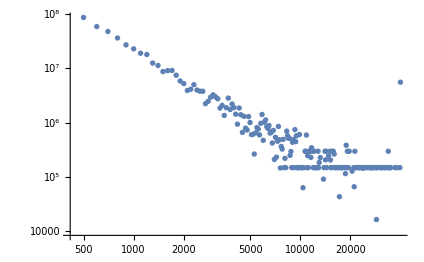

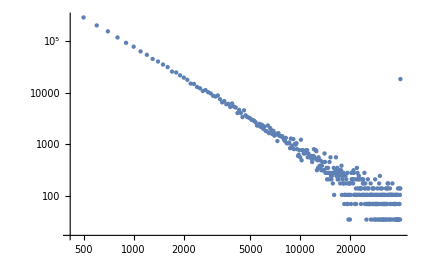

-Graphics-

```mathematica
sizes = {1177 ,4264 ,15443 ,28000 ,37323 ,51067 ,74908 ,93293 ,141819 ,237853 ,573344 ,2076744 ,7521945 ,27244995 ,98686787 ,223092956};

ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==223092956)&]],PlotRange->All]
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==51067)&]],PlotRange->All]

ListLogLogPlot[Map[Module[{x},x=#;Callout[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==x)&]],x]]&,sizes],PlotRange->All,Joined->True]
```

3377.54

4420.99

48828.2

{4421,1080,1168,6889,9501,48828,36987,26320,26823,24132,14042,1712,596,1158,1978,3378}

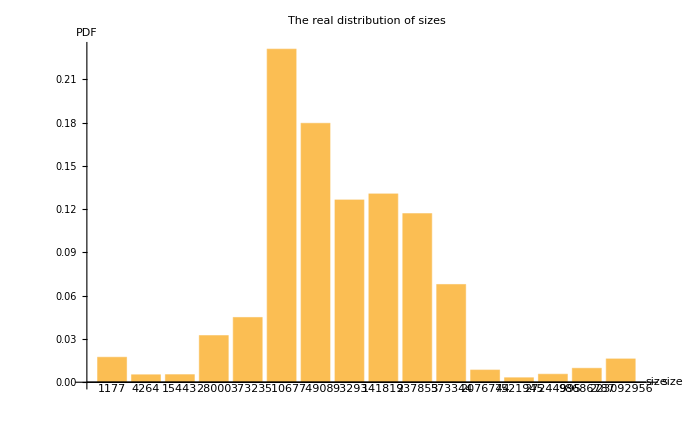

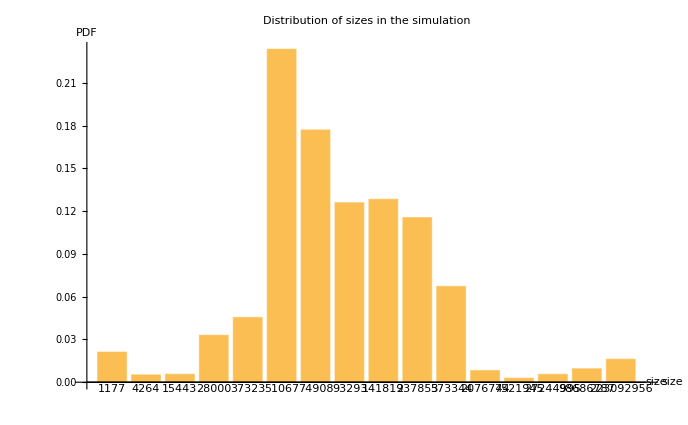

```mathematica
Total[Map[#[[3]]&,Select[data,(#[[1]]==223092956)&]]]/(223092956/1500)//N
Total[Map[#[[3]]&,Select[data,(#[[1]]==1177)&]]]/(1177/1500)//N

Total[Map[#[[3]]&,Select[data,(#[[1]]==51067)&]]]/(51067/1500)//N
d=Map[Module[{s},s=#;Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,sizes]
BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}]
BarChart[1/Total[d]*d,ChartLabels->sizes,PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]
```

```mathematica
data2
```

data2

```mathematica
Map[Module[{s},s=#;ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[data2,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->s,AxesLabel->{"Rate (Mbps)","Avg miss hop"}]]&,sizes]


ListLogLinearPlot[Map[Module[{x},x=#;Callout[Map[{#[[2]],#[[3]]}&,Select[data2,(#[[1]]==x)&]],x]]&,sizes],PlotRange->All,Joined->True]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==s$22323&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

Part::partd: Part specification data2⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of #1⟦1⟧==s$22323& does not exist.

Part::partw: Part 3 of #1⟦1⟧==s$22323& does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==s$22387&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of #1⟦1⟧==s$22387& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==s$22446&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==x$22992&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

Part::partd: Part specification data2⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of #1⟦1⟧==x$22992& does not exist.

Part::partw: Part 3 of #1⟦1⟧==x$22992& does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==x$23003&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of #1⟦1⟧==x$23003& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==x$23014&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

-Graphics-

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data2,(#[[1]]==223092956)&]],PlotRange->All]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==223092956&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

Part::partd: Part specification data2⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of #1⟦1⟧==223092956& does not exist.

Part::partw: Part 3 of #1⟦1⟧==223092956& does not exist.

-Graphics-

```mathematica
Mean[Map[{#[[2]],#[[3]]}&,Select[data2,(#[[1]]==1177)&]]][[2]]//N
```

Select::normal: Nonatomic expression expected at position 1 in Select[data2,#1⟦1⟧==1177&].

Part::partd: Part specification data2⟦2⟧ is longer than depth of object.

Part::partd: Part specification data2⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of #1⟦1⟧==1177& does not exist.

Part::partw: Part 3 of #1⟦1⟧==1177& does not exist.

Part::partw: Part 2 of Mean[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Mean[{}]⟦2⟧

```mathematica
ListPlot3D[data3,PlotRange->All]
```

ListPlot3D::arrayerr: data3 must be a valid array or a list of valid arrays.

ListPlot3D[data3,PlotRange→All]

Part::take: Cannot take positions 2 through -2 in {0.}.

Join::heads: Heads Part and List at positions 1 and 3 are expected to be the same.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

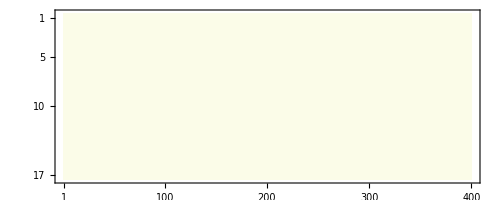

ListPlot3D::arrayerr: data3 must be a valid array or a list of valid arrays.

ListPlot3D[data3,Mesh→None,InterpolationOrder→0,PlotLabel→Avg Miss count,AxesLabel→{size (Bytes),rate (Mbps),miss count},PlotRange→{0,4}]

```mathematica
hashsize[size_]:=Position[sizes,size][[1]][[1]];
heatMap = ConstantArray[0,{17,40000/100}];
Map[((heatMap[[hashsize[#[[1]]],(#[[2]])/100]] = #[[3]]))&,data3];
MatrixPlot[heatMap,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->All,PlotLegends->Automatic]
Print[ListPlot3D[data3,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Miss count",AxesLabel->{"size (Bytes)","rate (Mbps)","miss count"},PlotRange->{0,4}]];
```

```mathematica
data3 //N
```

data3

```mathematica
Round[6.8]
```

7

```mathematica
ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==1177)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[1177] <> "\n number of pcks = " <> ToString[N[1177/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[(2.06* 10^9)/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT",Tiny],Automatic]}]
(2.06* 10^9)/10^6
```

-Graphics-

2060.

```mathematica
"size =  " <> ToString[1177]
```

size =  1177

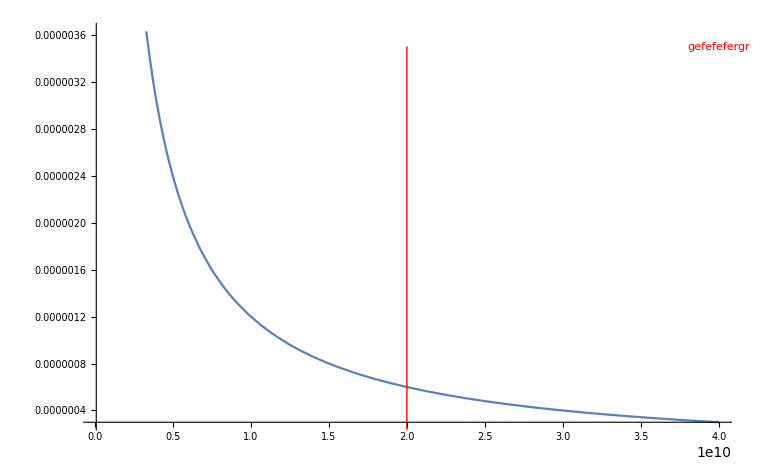

```mathematica
rate[rate_]:= ((1500.0*8.0)/rate);
Plot[rate[r],{r,100*10^6,40*10^9},Epilog->{Red,Line[Table[{2 10^10,i},{i,0,3.5 10^-6,10^-7}]],Text["gefefefergr",{4 10^10,3.5 10^-6}]}]
```

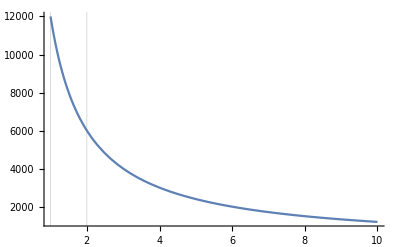

```mathematica
Plot[rate[r],{r,1,10},GridLines->{{1,2},{4,6}},PlotRange->All]
```

```mathematica
If[False == True,rtt = 5.8*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt
p=Map[Module[{s},s=#;ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT",Tiny],Automatic]}]]&,sizes];
```

2.06897×10^9

```mathematica
Labeled[p[[1]],"dfef"]
```

-Graphics-dfef